# Implementing a Tsetlin Machine Framework-- So Long, Neural Nets!

By: Dmitri Volkov

Mentor: Nikki Sigurdson

## Introduction

Machine learning is a field of research that has been growing in relevance throughout the past few years, and has had an impact in many areas in modern life. Although Neural Nets have been behind the majority of the push, learning algorithms such as Logistic Regression, Decision Trees, Monte Carlo Markov Chains, Nearest Neighbor, Support Vector Machines, and the like have also been useful. Now, another strong competitor can join their ranks: the Tsetlin Machine. The Tsetlin Machine is a type of machine learning that acts on binary data based on Tsetlin Automata, which were invented by Michael Lvovitch Tsetlin in the early 1960s. One of the advantages of Tsetlin Machines is that they work with Boolean operations on binary data, which is very fast compared to the calculus Neural Nets need to do. While a single Tsetlin Automaton is not very powerful, when many are used together the opposite can be true. Unfortunately, putting multiple Tsetlin Automata together resulted in the problem of a vanishing signal-to-noise ratio-- in other words, each Tsetlin Automaton optimized for itself instead of the whole, leading to an ineffective learning system. Fortunately, 2018 research by Ole-Christoffer Granmo has solved the vanishing signal-to-noise ratio problem and made Tsetlin Machines a viable competitor to Neural Nets and other machine learning algorithms. This computational essay presents a modular framework, written in the Wolfram Language, for creating and applying Tsetlin Machines.

## Tsetlin Automata

The building block of Tsetlin Machines is the Tsetlin Automaton, similar to the Neuron in Neural Nets. Here, Tsetlin Automatons are represented by a single integer (which holds their state).

A Tsetlin Automaton in state 3:

```mathematica
3
```

3

Tsetlin Automatons choose an action based on their state. If their state is less than or equal to a number (called a state identifier), then they choose action 1. Otherwise they choose action 2. The maximum state a Tsetlin Automaton can have is 2 * the state identifier. The TsetinAutomatonCalculateAction function takes a Tsetlin Automaton and a state identifier as input, and outputs a 1 or 2 corresponding to the action the Tsetlin Automaton chooses.

The TsetlinAutomatonCalculateAction function definition:

```mathematica
TsetlinAutomatonCalculateAction=
Compile[
{{ta,_Integer},{si,_Integer}},
If[
ta>si,
2,
1],
CompilationTarget->"C"]
```

CompiledFunction[…]

A Tsetlin Automaton in state 3 choosing action 1:

```mathematica
TsetlinAutomatonCalculateAction[3,3]
```

1

A Tsetlin Automaton in state 3 choosing action 2:

```mathematica
TsetlinAutomatonCalculateAction[3,2]
```

2

Approach is a utility function that takes three arguments: a current value, target value, and delta value. It outputs the current value shifted closer to the target value by the delta value.

The Approach function definition:

```mathematica
Approach=
Compile[
{{x,_Real},{y,_Real},{t,_Real}},
Which[
x==y,x,
x>y,x-t,
x<y,x+t],
CompilationTarget->"C"]
```

CompiledFunction[…]

```mathematica
Approach[3,10,4]
```

7.

Approach 10 ,starting from 1, by 5:

```mathematica
Approach[1,10,5]
```

6.

Approach 1, starting from 4, by 1:

```mathematica
Approach[4,1,1]
```

3

TsetlinAutomatonPunish and TsetlinAutomatonReward punish or reward a Tsetlin Automaton, given the automaton and the state identifier. In other words, they move a Tsetlin Automaton’s state closer or farther to the state which would cause the opposite action.

The TsetlinAutomatonPunish function definition.

```mathematica
TsetlinAutomatonPunish=
With[
{Approach=Approach},
Compile[
{{ta,_Integer},{si,_Integer}},
If[
ta>si,
IntegerPart@Approach[ta,1,1],
IntegerPart@Approach[ta,2*si,1]],
CompilationTarget->"C",
CompilationOptions->{"InlineCompiledFunctions" -> True}]]
```

CompiledFunction[…]

The TsetlinAutomatonReward function definition.

```mathematica
TsetlinAutomatonReward=
With[
{Approach=Approach},
Compile[{{ta,_Integer},{si,_Integer}},
If[
ta>si,
IntegerPart@Approach[ta,2*si,1],
IntegerPart@Approach[ta,1,1]],
CompilationTarget->"C",
CompilationOptions->{"InlineCompiledFunctions" -> True}]]
```

CompiledFunction[…]

Punish a Tsetlin Automaton in state 1, with state identifier 3. Because this corresponds to action 1, it will move it towards action 2, therefore raising the state.

```mathematica
TsetlinAutomatonPunish[3,3]
```

4

TsetlinAutomatonUpdate takes a state, a state identifier, and a number n such that n ∈ {1, 2} and updates the Tsetlin Automaton by rewarding it if it produced output equal output to n, or punishing it if it did not. It then outputs the Tsetlin Automaton.

The TsetlinAutomatonUpdate function definition:

```mathematica
TsetlinAutomatonUpdate=
With[
{TsetlinAutomatonCalculateAction=TsetlinAutomatonCalculateAction,
TsetlinAutomatonPunish=TsetlinAutomatonPunish,
TsetlinAutomatonReward=TsetlinAutomatonReward},
Compile[{{ta,_Integer},{si,_Integer},{n,_Integer}},
If[
TsetlinAutomatonCalculateAction[ta,si]==n,
TsetlinAutomatonReward[ta,si],
TsetlinAutomatonPunish[ta,si]],
CompilationTarget->"C",
CompilationOptions->{"InlineCompiledFunctions" -> True}]]
```

CompiledFunction[…]

Update a Tsetlin Automaton to learn to pick action 2.

```mathematica
TsetlinAutomatonUpdate[3,3,2]
```

4

By now, we have enough functions to implement a basic learning algorithm. The following bit of code learns which of two options gets a better result more often.

Train a Tsetlin Automaton via nesting TsetlinAutomatonUpdate:

```mathematica
ta1=NestList[
TsetlinAutomatonUpdate[
#,
3,
Position[
#,
TakeLargestBy[#,#&,1]⟦1⟧]⟦1⟧⟦1⟧&@{RandomVariate[NormalDistribution[0.75,.5]],RandomVariate[NormalDistribution[0.25,.5]]}]&,
4,10]
```

{4,3,4,3,2,1,1,2,1,2,1}

Plot the state of the newly trained Tsetlin Automaton’s over time. State 2 is above the straight line in the middle, state 1 is below.

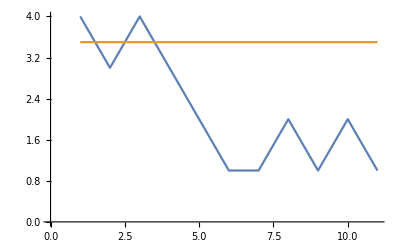

```mathematica
ListLinePlot[{ta1,Table[3.5,Length[ta1]]}]
```

Get the final action of ta1:

```mathematica
TsetlinAutomatonCalculateAction[ta1[[-1]],3]
```

1

TsetlinAutomatonWeightedReward and TsetlinAutomatonWeightedPunish are similar to TsetlinAutomatonReward and TsetlinAutomatonPunish, except that they also take a third argument. If the third argument is greater than a random real number from 0 to 1, then it rewards/punishes the Tsetlin Automaton (otherwise it does nothing). This is very important for later.

The TsetlinAutomatonWeightedReward function definition:

```mathematica
TsetlinAutomatonWeightedReward=
With[
{TsetlinAutomatonReward=TsetlinAutomatonReward},
Compile[
{{ta,_Integer},{si,_Integer},{pf,_Real}},
If[
RandomReal[]≤pf,
TsetlinAutomatonReward[ta,si],
ta],
CompilationTarget->"C",
CompilationOptions->{"InlineCompiledFunctions" -> True}]]
```

CompiledFunction[…]

The TsetlinAutomatonWeightedPunish function definition:

```mathematica
TsetlinAutomatonWeightedPunish=
With[
{TsetlinAutomatonPunish=TsetlinAutomatonPunish},
Compile[{{ta,_Integer},{si,_Integer},{pf,_Real}},
If[
RandomReal[]≤pf,
TsetlinAutomatonPunish[ta,si],
ta],
CompilationTarget->"C",
CompilationOptions->{"InlineCompiledFunctions" -> True}]]
```

CompiledFunction[…]

TsetlinAutomatonListInitialize is a function that, given a state identifier and number of automata, randomly initializes a list of Tsetlin Automata.

The function definition for TsetlinAutomatonListInitialize:

```mathematica
TsetlinAutomatonListInitialize[si_Integer,il_Integer]:=
Table[RandomInteger[]+si,il]
```

## Basic Structure of a Tsetlin Machine

The Tsetlin Machine is arranged hierarchically. At the lowest level, there are Tsetlin Automata. In a Tsetlin Machine, the Tsetlin Automata are responsible for figuring out which input to include and which input to exclude. Each Automata corresponds to one input. One level up, there are Tsetlin Clauses, which hold two lists-- one that holds the Tsetlin Automata that chose whether to include or exclude the input, and another that holds another set of Tsetlin Automata that chose whether to include or exclude the input negated. The Tsetlin Clause then applies the “AND” operation to all of the included inputs and outputs the result.

An input of {True, False, True} would be fed to a Tsetlin Clause like the following:

```mathematica
{{True,False,True},{False,True,False}}
```

{{True,False,True},{False,True,False}}

A Tsetlin Clause that includes the positive inputs, assuming state identifier 3:

```mathematica
TsetlinClause[{4,6,5},{2,3,1}]
```

TsetlinClause[{4,6,5},{2,3,1}]

The TsetlinClause head has the following 2 helper functions: TsetlinClauseGetPositive and TsetlinClauseGetNegative. These return the list of Tsetlin Automata corresponding to the positive and negative (negated) inputs, respectively.

The function definitions for TsetlinClauseGetPositive and TsetlinClauseGetNegative:

```mathematica
TsetlinClauseGetPositive[tc_TsetlinClause]:=tc[[1]]
```

```mathematica
TsetlinClauseGetNegative[tc_TsetlinClause]:=tc[[2]]
```

Getting the list of Tsetlin Automata that correspond to negated input:

```mathematica
TsetlinClauseGetNegative[
TsetlinClause[{1,2,3},{4,5,6}]]
```

{4,5,6}

A TsetlinClause also has the helper function TsetlinClauseInitialize, which takes two integer inputs: the state identifier and number of inputs. It outputs a randomly initialized TsetlinClause.

The function definition for TsetlinClauseInitialize:

```mathematica
TsetlinClauseInitialize[si_Integer,il_Integer]:=
Module[{
base=TsetlinAutomatonListInitialize[si,il]},
TsetlinClause[base,((2*si)-base)+1]]
```

One step up the hierarchy from a Tsetlin Clause is a Tsetlin Output. A TsetlinOutput head has two arguments: a list of TsetlinClauses and a function (which should take a list of Booleans as input and output a Boolean):

An example of a TsetlinOutput:

```mathematica
TsetlinOutput[
{
TsetlinClause[{2,3,4},{1,5,6}],
TsetlinClause[{3,4,3},{4,3,4}]},
Or@@#&]
```

TsetlinOutput[{TsetlinClause[{2,3,4},{1,5,6}],TsetlinClause[{3,4,3},{4,3,4}]},Or@@#1&]

The TsetlinOutput head has the following helper functions: TsetlinOutputGetClauses and TsetlinOutputGetFunction. Given a TsetlinOutput, the return the list of clauses or the function, respectively.

The function definitions for TsetlinOutputGetClauses and TsetlinOutputGetFunction:

```mathematica
TsetlinOutputGetClauses[to_TsetlinOutput]:=to[[1]]
```

```mathematica
TsetlinOutputGetFunction[to_TsetlinOutput]:=to[[2]]
```

Getting the clauses of a TsetlinOutput:

```mathematica
TsetlinOutputGetClauses[
TsetlinOutput[
{
TsetlinClause[{1,2,3},{4,5,6}],
TsetlinClause[{2,4,6},{8,10,12}]},
Or@@#&]]
```

{TsetlinClause[{1,2,3},{4,5,6}],TsetlinClause[{2,4,6},{8,10,12}]}

Getting the function of a TsetlinOutput:

```mathematica
TsetlinOutputGetFunction[
TsetlinOutput[
{
TsetlinClause[{1,2,3},{4,5,6}],
TsetlinClause[{2,4,6},{8,10,12}]},
Or@@#&]]
```

Or@@#1&

TsetlinOutput has an initializer too: TsetlinOutputInitialize. It takes 4 arguments: the state identifier, the length of the input, the desired number of clauses for the given output, and the output function.

The function definition for TsetlinOutputInitialize:

```mathematica
TsetlinOutputInitialize[si_Integer,il_Integer,nc_Integer, f_]:=
TsetlinOutput[
Table[
TsetlinClauseInitialize[si,il],
nc],
f]
```

A function useful for analyzing trained Tsetlin Machines is TsetlinOutputCalculateFormula, which takes a TsetlinOutput and state identifier, and outputs a propositional formula that represents how the TsetlinOutput calculates its’ results (the numbers refer to the inputs, the negative numbers to the negated inputs):

The function definition for TsetlinOutputCalculateFormula:

```mathematica
TsetlinOutputCalculateFormula[to_TsetlinOutput,si_Integer]:=
TsetlinOutputGetFunction[to][
And@@{
And@@((MapThread[
((TsetlinAutomatonCalculateAction[#1,si]-1)*#2)&,
{
TsetlinClauseGetPositive[#],
Range@Length@TsetlinClauseGetPositive[#]}]&@
TsetlinOutputGetClauses[to]⟦#⟧)/.{0->Nothing}),
And@@((MapThread[
(-(TsetlinAutomatonCalculateAction[#1,si]-1)*#2)&,
{
TsetlinClauseGetNegative[#],
Range@Length@TsetlinClauseGetNegative[#]}]&@
TsetlinOutputGetClauses[to]⟦#⟧)/.{0->Nothing})}&/@
Range@Length@TsetlinOutputGetClauses[to]]
```

Running TsetlinOutputCalculateFormula on a newly generated TsetlinOutput:

```mathematica
TsetlinOutputCalculateFormula[
TsetlinOutputInitialize[3,3,2,TsetlinUtilityOr],
3]
```

(1&&2&&-3)||(3&&-1&&-2)

One more step up the hierarchy, and we have a complete Tsetlin Machine! The TsetlinMachine head takes 2 arguments: a list of TsetlinOutputs and a state identifier.

An example of a complete TsetlinMachine:

```mathematica
tm1=TsetlinMachine[
{
TsetlinOutput[
{TsetlinClause[{2,4},{2,4}],
TsetlinClause[{1,4},{1,4}]},
Or@@#&],
TsetlinOutput[
{TsetlinClause[{6,3},{1,3}],
TsetlinClause[{2,6},{4,5}]},
Or@@#&]},
3]
```

TsetlinMachine[{TsetlinOutput[{TsetlinClause[{2,4},{2,4}],TsetlinClause[{1,4},{1,4}]},Or@@#1&],TsetlinOutput[{TsetlinClause[{6,3},{1,3}],TsetlinClause[{2,6},{4,5}]},Or@@#1&]},3]

The TsetlinMachine head has 2 helper functions: TsetlinMachineGetOutputs and TsetlinMachineGetStateIdentifier. They each take a TsetlinMachine as input, and return the list of outputs or the state identifier, respectively.

The function definitions for TsetlinMachineGetOutputs and TsetlinMachineStateIdentifier:

```mathematica
TsetlinMachineGetOutputs[tm_TsetlinMachine]:=tm[[1]]
```

```mathematica
TsetlinMachineGetStateIdentifier[tm_TsetlinMachine]:=tm[[2]]
```

Get the outputs of a TsetlinMachine:

```mathematica
TsetlinMachineGetOutputs[tm1]
```

{TsetlinOutput[{TsetlinClause[{2,4},{2,4}],TsetlinClause[{1,4},{1,4}]},Or@@#1&],TsetlinOutput[{TsetlinClause[{6,3},{1,3}],TsetlinClause[{2,6},{4,5}]},Or@@#1&]}

Get the state identifier of a TsetlinMachine:

```mathematica
TsetlinMachineGetStateIdentifier[tm1]
```

3

There also is an initializer for TsetlinMachines which takes 4 inputs: the state identifier integer, the length of the inputs, the number of clauses per output, and a list of output functions.

The function definition for TsetlinMachineInitialize:

```mathematica
TsetlinMachineInitialize[si_Integer,il_Integer,nc_Integer,lf_List]:=
TsetlinMachine[
Map[
TsetlinOutputInitialize[
si,
il,
nc,
#]&,
lf],
si]
```

## Using a Tsetlin Machine

Before a TsetlinMachine can be trained, it needs to be able to be used. For the purposes of developing functions that apply a TsetlinMachine, we still can use one that is already trained. Take the following TsetlinMachine which has been trained to the XOR operation:

Create a Tsetlin machine that calculates XOR with 2 inputs:

```mathematica
tm2=TsetlinMachine[
{
TsetlinOutput[
{
TsetlinClause[
{4,2},
{1,4}],
TsetlinClause[
{3,6},
{5,2}]},
Or@@#&]},
3]
```

TsetlinMachine[{TsetlinOutput[{TsetlinClause[{4,2},{1,4}],TsetlinClause[{3,6},{5,2}]},Or@@#1&]},3]

Let's again work from the bottom up. TsetlinClauseCalculateIncludedInputs takes a TsetlinClause, state identifier, and list of inputs, figures which ones are included based on their respective Tsetlin Automaton, and outputs a list of the included inputs.

The function definition for TsetlinClauseCalculateIncludedInputs:

```mathematica
TsetlinClauseCalculateIncludedInputs[tc_TsetlinClause,si_Integer,li_List]:=
Last/@
Select[
Join[
Transpose[{
(TsetlinAutomatonCalculateAction[#,si]&/@TsetlinClauseGetPositive[tc]),
li}],
Transpose[{
(TsetlinAutomatonCalculateAction[#,si]&/@TsetlinClauseGetNegative[tc]),
Not/@li}]],
#[[1]]==2&]
```

Applying TsetlinClauseCalculateIncludedInputs to the first clause in the XOR TsetlinMachine above, with input {True, False}:

```mathematica
TsetlinClauseCalculateIncludedInputs[
TsetlinOutputGetClauses[
TsetlinMachineGetOutputs[tm2][[1]]][[1]],
TsetlinMachineGetStateIdentifier[tm2],
{True,False}]
```

{True,True}

TsetlinClauseCalculateResult takes a TsetlinClause, state identifier, and a list of inputs and figures out the output of the TsetlinClause (it ANDs the included inputs).

The function definition for TsetlinClauseCalculateResult.

```mathematica
TsetlinClauseCalculateResult[tc_TsetlinClause,si_Integer,li_List]:=
Fold[
And,
True,
TsetlinClauseCalculateIncludedInputs[tc,si,li]]
```

Applying TsetlinClauseCalculateResult to the first clause in the XOR TsetlinMachine above, with input {True, False} :

```mathematica
TsetlinClauseCalculateResult[
TsetlinOutputGetClauses[
TsetlinMachineGetOutputs[tm2][[1]]][[1]],
TsetlinMachineGetStateIdentifier[tm2],
{True,False}]
```

True

TsetlinOutputCalculateResult takes a TsetlinOutput, state identifier, and list of inputs as it’s arguments. It returns the result of fold-applying the function of the TsetlinOutput to the TsetlinClause outputs calculated with the given state identifier and input.

The function definition for TsetlinOutputCalculateResult:

```mathematica
TsetlinOutputCalculateResult[to_TsetlinOutput,si_Integer,li_List]:=
TsetlinOutputGetFunction[to][
Map[
TsetlinClauseCalculateResult[#,si,li]&,
TsetlinOutputGetClauses[to]]]
```

Applying TsetlinOutputCalculateResult to the first output in the XOR TsetlinMachine above, with input {True, False} :

```mathematica
TsetlinOutputCalculateResult[
TsetlinMachineGetOutputs[tm2][[1]],
TsetlinMachineGetStateIdentifier[tm2],
{True,False}]
```

True

TsetlinMachineCalculateResult takes a TsetlinMachine and a list of inputs as input, and outputs a list of the outputs. This is the way to apply trained Tsetlin machines.

The function definition for TsetlinMachineCalculateResult:

```mathematica
TsetlinMachineCalculateResult[tm_TsetlinMachine,li_List]:=
Map[
TsetlinOutputCalculateResult[
#,
TsetlinMachineGetStateIdentifier[tm],
li]&,
TsetlinMachineGetOutputs[tm]]
```

Applying TsetlinMachineCalculateResult to the first output in the XOR TsetlinMachine above, with input {True, False} :

```mathematica
TsetlinMachineCalculateResult[
tm2,
{True,False}]
```

{True}

## Providing Feedback to a Tsetlin Machine

This is where things begin to get more difficult, and as of the writing of this, there is probably something wrong with my code in this section. So, how Tsetlin Machines train is via feedback (similar in idea but very different in implementation to backpropagation in Neural Nets). There are two types of feedback for Tsetlin Machines, called type 1 and type 2. The best way I can describe the difference between the difference between the two is as follows: Type 1 feedback does most of the work, and type 2 cleans up what type 1 could not. Very vague, I know. This learning algorithm was derived from propositional formulas, which can be found in the original Tsetlin Machine paper.

I use 5 different feedback functions, again working from the bottom up. The first two apply type 1 or type 2 feedback to an individual Tsetlin Automaton. The first four inputs for each function is the same: an integer representing a Tsetlin Automaton, the state identifier, the input that corresponds to the automaton, and the output of the clause that the automaton is a member of. Type 1 feedback’s 5th argument is an s-value (in other words, the precision). Type 2 feedback’s 5th argument is a Boolean that is True if the automaton corresponds to an original input, or False for a negated one.

The function definition for TsetlinAutomatonType1Feedback:

```mathematica
TsetlinAutomatonType1Feedback[ta_Integer,si_Integer,i_?BooleanQ,co_?BooleanQ,s_?NumericQ]:=
If[
co (* clause output is 1 or 0? *),
If[
i, (* input is 1 or 0 *)
If[
(ta>si), (* input is included or excluded *)
TsetlinAutomatonWeightedReward[ta,si,((s-1)/s)],
TsetlinAutomatonWeightedPunish[ta,si,((s-1)/s)]],
If[
(ta>si), (* innput is included ot excluded *)
ta,
TsetlinAutomatonWeightedReward[ta,si,(1/s)]]],
If[
(ta>si), (* input is included or excluded *)
TsetlinAutomatonWeightedPunish[ta,si,(1/s)],
TsetlinAutomatonWeightedReward[ta,si,(1/s)]]]
```

The function definition for TsetlinAutomatonType2Feedback:

```mathematica
TsetlinAutomatonType2Feedback[ta_Integer,si_Integer,i_?BooleanQ,co_?BooleanQ,it_?BooleanQ]:=
If[ 
(co==True),
If[
Not[i],
If[
Not[(TsetlinAutomatonCalculateAction[ta,si]==2)],
If[
it,
TsetlinAutomatonPunish[ta,si],
ta],
ta],
If[
Not[(TsetlinAutomatonCalculateAction[ta,si]==2)],
If[
Not[it],
TsetlinAutomatonPunish[ta,si],
ta],
ta],
ta],
ta]
```

Apply TsetlinAutomatonType1Feedback to an arbitrary automaton:

```mathematica
TsetlinAutomatonType1Feedback[
3,
3,
True,
False,
3.6]
```

2

Apply TsetlinAutomatonType2Feedback to an arbitrary automaton:

```mathematica
TsetlinAutomatonType2Feedback[
5,
3,
False,
False,
False]
```

5

You can also apply Type 1 and Type 2 feedback to a clause at a time. The type 1 feedback function takes a TsetlinClause, state identifier, input list, and s-value. The type 2 feedback function has all the same arguments except for the s-value.

The function definition for TsetlinClauseType1Feedback:

```mathematica
TsetlinClauseType1Feedback[tc_TsetlinClause,si_Integer,il_List,s_?NumericQ]:=
TsetlinClause[
MapThread[
TsetlinAutomatonType1Feedback[
#1,
si,
#2,
TsetlinClauseCalculateResult[tc,si,il],
s]&,
{TsetlinClauseGetPositive[tc],
il}],
MapThread[
TsetlinAutomatonType1Feedback[
#1,
si,
#2,
TsetlinClauseCalculateResult[tc,si,il],
s]&,
{TsetlinClauseGetNegative[tc],
Not/@il}]]
```

The function definition for TsetlinClauseType2Feedback:

```mathematica
TsetlinClauseType2Feedback[tc_TsetlinClause,si_Integer,il_List]:=
TsetlinClause[
MapThread[
TsetlinAutomatonType2Feedback[
#1,
si,
#2,
TsetlinClauseCalculateResult[tc,si,il],
True]&,
{TsetlinClauseGetPositive[tc],
il}],
MapThread[
TsetlinAutomatonType2Feedback[
#1,
si,
#2,
TsetlinClauseCalculateResult[tc,si,il],
False]&,
{TsetlinClauseGetNegative[tc],
Not/@il}]]
```

TsetlinOutputFeedback applies both kinds of feedback to the TsetlinClauses of a TsetlinOutput, according to some function (called a feedbackDecider). It takes 6 arguments: a TsetlinOutput,  a state identifier, the input list, the desired output of the TsetlinOutput, an s-value, and a feedbackDecider function. The feedbackDecider is written by the user and should accept 6 arguments: the TsetlinOutput currently being processed, the index of the clause being trained (in the list of TsetlinClauses in the output), the state identifier, the input list, the desired output, and the s-value. The feedbackDecider should return a value from 0 to 2, denoting the type of feedback the clause at the given index in the TsetlinOutput should receive (0 means no feedback).

The function definition for TsetlinOutputFeedback:

```mathematica
TsetlinOutputFeedback[to_TsetlinOutput,si_Integer,il_List,do_?BooleanQ,s_?NumericQ,fd_]:=
TsetlinOutput[
ParallelMap[
{(TsetlinOutputGetClauses[to][[#]]),
TsetlinClauseType1Feedback[
(TsetlinOutputGetClauses[to][[#]]),
si,
il,
s],
TsetlinClauseType2Feedback[
(TsetlinOutputGetClauses[to][[#]]),
si,
il]}[[(fd[to,#,si,il,do,s]+1)]]&,
Range[Length@TsetlinOutputGetClauses[to]]
],
TsetlinOutputGetFunction[to]]
```

TsetlinMachineFeedback takes 5 arguments : a TsetlinMachine, a list of inputs, the corresponding list of outputs, an s - value, and a feedbackDecider. Output is a TsetlinMachine that has been trained on the given input list and output list.

The function definition for TsetlinMachineFeedback:

```mathematica
TsetlinMachineFeedback[tm_TsetlinMachine,il_List,ol_List,s_?NumericQ,fd_]:=
TsetlinMachine[
MapThread[
TsetlinOutputFeedback[
#1,
TsetlinMachineGetStateIdentifier[tm],
il,
#2,
s,
fd]&,
{TsetlinMachineGetOutputs[tm],
ol}],
TsetlinMachineGetStateIdentifier[tm]]
```

Applying TsetlinMachineFeedback to try to train a TsetlinMachine to learn XOR:

```mathematica
TsetlinMachineFeedback[
TsetlinMachineInitialize[
3,
2,
2,
{Or@@#&}],
{True,False},
{True},
3.5,
RandomInteger[]+1&]
```

TsetlinMachine[{TsetlinOutput[{TsetlinClause[{3,3},{4,4}],TsetlinClause[{4,4},{3,4}]},Or@@#1&]},3]

## Tsetlin Machine Utility Functions

These functions, while not strictly necessary for a functional Tsetlin Machine, are convenient to use when actually training a machine. They are used later, but will be defined and explained here.

TsetlinUtilityAlternatingSum takes a single list of numbers as its argument. Say the list is {1, 2, 3, 4, 5}. TsetlinUtilityAlternatingSum would turn the list into the following series: 1 - 2 + 3 - 4 + 5. It would then evaluate that series for a result of 3.

The function definition for TsetlinUtilityAlternatingSum:

```mathematica
TsetlinUtilityAlternatingSum[lc_List]:=
Total[lc[[;;;;2]]]-Total[lc[[2;;;;2]]]
```

Apply TsetlunUtilityAlternatingSum to the list {1, 2, 3, 4, 5}:

```mathematica
TsetlinUtilityAlternatingSum[{1,2,3,4,5}]
```

3

TsetlinUtilityOutputFunction can be used as an output function for TsetlinOutputs. It replaces True and False with 1s and 0s, then finds the alternating sum. It then returns True if this value is greater than or equal to 0, and False otherwise.

The function definition for TsetlinUtilityOutputFunction:

```mathematica
TsetlinUtilityOutputFunction[lc_List]:=
(TsetlinUtilityAlternatingSum[lc/.{True->1,False->0}]≥0)
```

Apply TsetlunUtilityOutputFunction to the list {True, True, False, True}, which should output False:

```mathematica
TsetlinUtilityOutputFunction[{True,True,False,True}]
```

False

TsetlinUtilityFeedbackDecider is the base for a feedbackDecider. It takes 7 inputs: the TsetlinOutput currently being trained, the index of the clause being currently processed, the state identifier, the list of inputs currently being trained on, the desired output, the s-value (precision), and a T-value (threshold). In practical use, it’s first 6 arguments are filled with slots 1 through 6 (#1,#2,...) and it’s 7th argument is the T-value (and it is followed by a &).

The function definition for TsetlinUtilityFeedbackDecider:

```mathematica
TsetlinUtilityFeedbackDecider[to_TsetlinOutput,ci_Integer,si_Integer,il_List,do_?BooleanQ,s_?NumericQ,t_Integer]:=
If[
do==True,
If[
RandomReal[]≤
((t-Max[
-t,
Min[
t,
TsetlinUtilityAlternatingSum[
((TsetlinClauseCalculateResult[
#,
si,
il
]&/@
TsetlinOutputGetClauses[to])/.{True->1,False->0})]]])/
2t),
2-Mod[ci,2],
0],
If[
RandomReal[]≤
((t+Max[
-t,
Min[
t,
TsetlinUtilityAlternatingSum[
((TsetlinClauseCalculateResult[
#,
si,
il
]&/@
TsetlinOutputGetClauses[to])/.{True->1,False->0})]]])/
2t),
2-Mod[ci+1,2],
0]]
```

TsetlinUtilityOr applies the Or function to a list (normally it can only be applied to a sequence).

The function definition for TsetlinUtilityOr:

```mathematica
TsetlinUtilityOr[l_List]:=
Or@@l
```

TsetlinUtilityOrFeedbackDecider is a feedbackDecider base to be used with a machine that uses TsetlinUtilityOr as its’ output function Similar to TsetlinUtilityFeedbackDecider, the first 6 arguments should be slots and the 7th should be a threshold.

The function for TsetlinUtilityOrFeedbackDecider:

```mathematica
TsetlinUtilityOrFeedbackDecider[to_TsetlinOutput,ci_Integer,si_Integer,il_List,do_?BooleanQ,s_?NumericQ,t_Integer]:=
If[
do==True,
If[
RandomReal[]≤
(t-Min[t,
Total[(TsetlinClauseCalculateResult[
#,
si,
il]&/@
TsetlinOutputGetClauses[to])/.{True->1,False->0}]])/2t,
1,
0],
If[
RandomReal[]≤
(t+Min[t,
Total[(TsetlinClauseCalculateResult[
#,
si,
il]&/@
TsetlinOutputGetClauses[to])/.{True->1,False->0}]])/2t,
2,
0]]
```

## “Tset”ing and Training a Tsetlin Machine

“Tset” is the beginning of “Tsetlin” and is just “test” with the middle two letters swapped, get it?
Sorry.

Being able to test a Tsetlin Machine is important when training, to make sure that the Tsetlin Machine is actually learning. TsetlinMachineTest takes a TsetlinMachine, list of input lists, and list of output lists as its arguments. It returns the percentage of input-output pairs that the TsetlinMachine correctly predicted. It has three options: EchoTestResults (False by default, but will echo the test results if made true), ReturnTestResults (True by default, but if false will return the TsetlinMachine it was given as an argument instead), and SowTestResults (False by default, bu if true it will Sow the test results).

The function definition for TsetlinMachineTest:

```mathematica
TsetlinMachineTest[tm_TsetlinMachine,ill_List,oll_List,OptionsPattern[{EchoTestResults-> False,ReturnTestResults-> True,SowTestResults-> False}]]:=
Module[{f=
(N[Total@
(MapThread[
(TsetlinMachineCalculateResult[
tm,
#1]==#2)&,
{ill,oll}]/.{False->0,True->1})])/
(Length@ill)},
(If[
OptionValue[EchoTestResults]==True,
Echo[f,"Percent correct:"]];
If[
OptionValue[SowTestResults] == True,
Sow[f]];
If[
OptionValue[ReturnTestResults] == True,
Return[f],
Return[tm]])]
```

Testing a newly-initialized Tsetlin Machine on XOR:

```mathematica
TsetlinMachineTest[
TsetlinMachineInitialize[
3,
2,
2,
{Or@@#&}],
{{True,True},
{True,False}},
{{False},{True}},EchoTestResults->True]
```

Percent correct: 1.

1.

TsetlinMachineTrain takes 8 inputs: a TsetlinMachine, a list of training input lists, a list of training output lists, a list of testing input lists, a list of testing output lists, an s-value, a feedbackDecider, and a stop criteria. Output is a trained TsetlinMachine. A stop criteria  can be one of the following: a real number less than or equal to 1 (representing goal accuracy), an integer 1 or greater (representing number of times to train), a real number 1 or greater (representing seconds to train). It has the same options as TsetlinMachineTest.

The function definition for TsetlinMachineTrain:

```mathematica
TsetlinMachineTrain[tm_TsetlinMachine,ill_List,oll_List,till_List,toll_List,s_?NumericQ,fd_,sc_?NumericQ,OptionsPattern[{EchoTestResults-> False,ReturnTestResults-> False,SowTestResults-> False}]]:=
(looper=
Which[
IntegerQ[sc],0,
sc>1,AbsoluteTime[]];
NestWhile[
({trainInput,trainOutput}=RandomChoice@Transpose@{ill,oll};
TsetlinMachineFeedback[
TsetlinMachineTest[#1,till,toll,ReturnTestResults->False,EchoTestResults->OptionValue[EchoTestResults],SowTestResults->OptionValue[SowTestResults]],
trainInput,
trainOutput,
s,
fd])&,
tm,
Which[
IntegerQ[sc],looper++<sc,
sc>1,AbsoluteTime[]-looper<sc,
sc≤1,TsetlinMachineTest[#,till,toll]<sc]&])
```

## Actually Training a Tsetlin Machine

The first demonstration of the use of a TsetlinMachine will be on the simple 2-input XOR function.

Train a TsetlinMachine on XOR:

```mathematica
tmXor=
TsetlinMachineTrain[
TsetlinMachineInitialize[
3,
2,
2,
{TsetlinUtilityOr}],
{{False,False},{False,True},{True,False},{True,True}},
{{False},{True},{True},{False}},
{{False,False},{False,True},{True,False},{True,True}},
{{False},{True},{True},{False}},
9,
TsetlinUtilityOrFeedbackDecider[#1,#2,#3,#4,#5,#6,2]&,
1.00,
EchoTestResults-> False]
```

TsetlinMachine[{TsetlinOutput[{TsetlinClause[{3,6},{5,2}],TsetlinClause[{6,1},{2,4}]},TsetlinUtilityOr]},3]

Show the results of applying the TsetlinMachine for all the possible inputs of XOR:

```mathematica
TsetlinMachineCalculateResult[tmXor,#]&/@{{False,False},{False,True},{True,False},{True,True}}
```

{{False},{True},{True},{False}}

Show the formula that the Tsetlin Machine learned:

```mathematica
TsetlinOutputCalculateFormula[
TsetlinMachineGetOutputs[tmXor]⟦1⟧,
3]
```

(2&&-1)||(1&&-2)

The second demonstration of the use of a TsetlinMachine will be on the MNIST dataset:

Import the data:

```mathematica
mnist=ResourceObject["MNIST"]
```

ResourceObject[…]

Extract and format the training data:

```mathematica
mnistTrainData=ResourceData[mnist,"TrainingData"]//Map[(Flatten@ImageData@Binarize[#⟦1⟧]/.{0->False,1->True})->(IntegerDigits[#⟦2⟧,2,4]/.{0->False,1->True})&,#]&
```

$Aborted

Extract and format the testing data:

```mathematica
mnistTestData=ResourceData[mnist,"TestData"]//Map[(Flatten@ImageData@Binarize[#⟦1⟧]/.{0->False,1->True})->(IntegerDigits[#⟦2⟧,2,4]/.{0->False,1->True})&,#]&
```

{1}
 |  |  |  |

Train the TsetlinMachine:

```mathematica
TsetlinMachineTrain[
TsetlinMachineInitialize[
128,
784,
2000,
{TsetlinUtilityFeedbackDecider,TsetlinUtilityFeedbackDecider,TsetlinUtilityFeedbackDecider,TsetlinUtilityFeedbackDecider}],
#⟦1⟧&/@mnistTrainData,
#⟦2⟧&/@mnistTrainData,
#⟦1⟧&/@mnistTestData,
#⟦2⟧&/@mnistTestData,
10.0,
TsetlinUtilityFeedbackDecider[#1,#2,#3,#4,#5,#6,50]&,
400,
EchoTestResults->True]
```